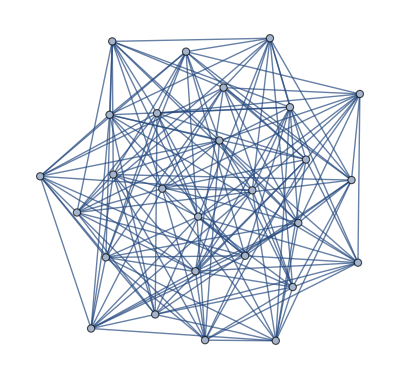

```mathematica
JR27b=ImportString["Z}q|vBOgkiPeaqWMiJ`FLDXsKzoUzR{@h}@IQJOqQdHClAfC{AvHDqUaPuFg", "Graph6"]
```

```mathematica
EdgeCount@JR27b
```

162

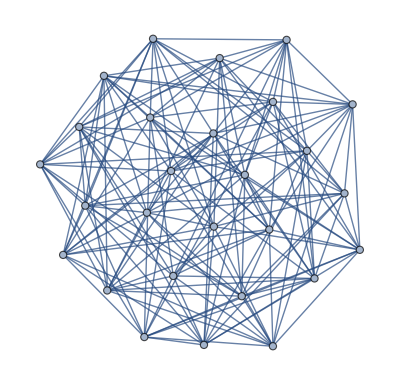

```mathematica
JR27c=ImportString["Z~rMDUidkmSdeTYwL[AkqTeGpMgXm`a]cKukX@RaoDkeEDZBQTM?skZ_ThMw", "Graph6"]
```

```mathematica
EdgeCount@JR27c
```

162

```mathematica
GraphData["VertexTransitive",27]
```

{{CompleteTripartite,{9,9,9}},DoyleGraph,{Empty,27},{GeneralizedQuadrangle,{2,4}},{GeneralizedQuadrangleMinusSpread,{{2,4},1}},{GeneralizedQuadrangleMinusSpread,{{2,4},2}},GrayConfigurationMengerDual,{Hamming,{3,3}},{Quartic,{27,1}},{Rook,{3,9}},{RookComplement,{3,9}},SchlaefliGraph,{TorusGrid,{3,9}}}

```mathematica
GraphData[#,{"EdgeCount","VertexCount"}]&/@GraphData["VertexTransitive",27]
```

{{243,27},{54,27},{0,27},{135,27},{108,27},{108,27},{81,27},{81,27},{54,27},{135,27},{216,27},{216,27},{54,27}}

```mathematica
Do[G=GraphData["VertexTransitive",27][[5;;6]][[i]];
Print[IsomorphicGraphQ[JR27,GraphData[G]]],{i,1,2}]
```

False

True

```mathematica
JRGD=GraphData["VertexTransitive",27][[6]]
```

{GeneralizedQuadrangleMinusSpread,{{2,4},2}}

```mathematica
GraphData[JRGD,"FractionalChromaticNumber"]
```

9/2

```mathematica
GraphData[JRGD,"AlternateStandardNames"]
```

{}

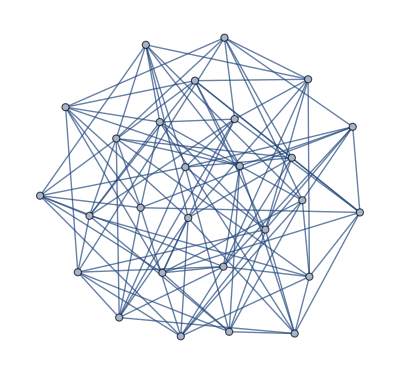

```mathematica
GraphPlot[GraphData[JRGD,"Edges","Rule"]]
```

```mathematica
GraphPlot[GraphData[JRGD,"AdjacencyMatrix"],VertexCoordinates->GraphData[JRGD,"VertexCoordinates"]]
```

GraphPlot[SparseArray[…],VertexCoordinates→Missing[NotAvailable]]

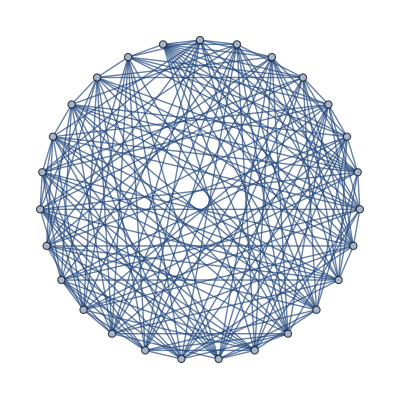

```mathematica
JR27b=GraphComplement@ImportString["Z}q|vBOgkiPeaqWMiJ`FLDXsKzoUzR{@h}@IQJOqQdHClAfC{AvHDqUaPuFg", "Graph6"]
```

```mathematica
EdgeCount@JR27b
```

189

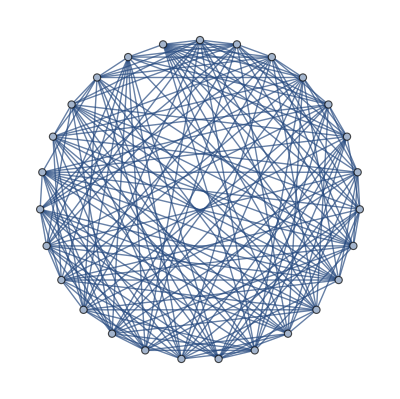

```mathematica
JR27c=GraphComplement@ImportString["Z~rMDUidkmSdeTYwL[AkqTeGpMgXm`a]cKukX@RaoDkeEDZBQTM?skZ_ThMw", "Graph6"]
```

```mathematica
EdgeCount@JR27c
```

189

```mathematica
GraphData["VertexTransitive",27]
```

{{CompleteTripartite,{9,9,9}},DoyleGraph,{Empty,27},{GeneralizedQuadrangle,{2,4}},{GeneralizedQuadrangleMinusSpread,{{2,4},1}},{GeneralizedQuadrangleMinusSpread,{{2,4},2}},GrayConfigurationMengerDual,{Hamming,{3,3}},{Quartic,{27,1}},{Rook,{3,9}},{RookComplement,{3,9}},SchlaefliGraph,{TorusGrid,{3,9}}}

```mathematica
GraphData[#,{"EdgeCount","VertexCount"}]&/@GraphData["VertexTransitive",27]
```

{{243,27},{54,27},{0,27},{135,27},{108,27},{108,27},{81,27},{81,27},{54,27},{135,27},{216,27},{216,27},{54,27}}

```mathematica
Do[G=GraphData["VertexTransitive",27][[5;;6]][[i]];
Print[IsomorphicGraphQ[JR27,GraphData[G]]],{i,1,2}]
```

False

True

```mathematica
JRGD=GraphData["VertexTransitive",27][[6]]
```

{GeneralizedQuadrangleMinusSpread,{{2,4},2}}

```mathematica
GraphData[JRGD,"FractionalChromaticNumber"]
```

9/2

```mathematica
GraphData[JRGD,"AlternateStandardNames"]
```

{}

```mathematica
GraphPlot[GraphData[JRGD,"Edges","Rule"]]
```

-Graphics-

```mathematica
GraphPlot[GraphData[JRGD,"AdjacencyMatrix"],VertexCoordinates->GraphData[JRGD,"VertexCoordinates"]]
```

GraphPlot[SparseArray[…],VertexCoordinates→Missing[NotAvailable]]